## Ray

### Prerequisites

```mathematica
Protect[CalculateFinalTime];
```

```mathematica
(*critical curve on the λ-η plane*)
λc[rc_,a_]:=a+(rc (2 a^2+(-3+rc) rc))/(a-a rc);
ηc[rc_,a_]:=-(rc^3 (-4 a^2+(-3+rc)^2 rc))/(a^2 (-1+rc)^2);
```

```mathematica
(*critical curve on the image plane*)
αc[rc_,a_,θo_]:=-Csc[θo] λc[rc,a];
βc[rc_,a_,θo_]:=√(a^2 Cos[θo]^2+ηc[rc,a]-Cot[θo]^2 λc[rc,a]^2);
```

```mathematica
(*range of rc along the critical curve*)
rcRange[a_]:=Module[{rdown,rup},
rdown=4 Cos[ArcCos[-a]/3]^2;
rup=4 Cos[ArcCos[a]/3]^2;
{rdown,rup}];
```

```mathematica
(*transform (rc,d) to (λ,q), where q=√η*)
rcd$to$λq[a_,rc_,d_]:=Module[{λc0,ηc0,qc,nλq},
λc0=λc[rc,a];
ηc0=ηc[rc,a];
qc=√ηc0;
nλq=1/(√((-3+rc)^2/(a^2 (-1+rc)^2)+ηc0/rc^4)){(3-rc)/(a (-1+rc)),(√ηc0)/rc^2} ;
{λc0,qc}+d nλq];
```

```mathematica
(*transform (λ,q) to (rc,d)*)
λq$to$rcd[a_,λ_,q_]:=Module[{sol,res$rc,res$d},
sol=FindRoot[(4 (-1+rc) √(-(rc^3 ((-3+rc)^2 rc-4 a^2))/((-1+rc)^2 a^2)))(λ-a-(rc ((-3+rc) rc+2 a^2))/(a-rc a))-(5 (3-rc) rc^2)(q-√(-(rc^3 ((-3+rc)^2 rc-4 a^2))/((-1+rc)^2 a^2)))==0,{rc,3}];
res$rc=sol[[1,2]];
res$d=√((q-√ηc[res$rc,a])^2+(λ-λc[res$rc,a])^2);
{res$rc,res$d}
]
```

```mathematica
(*transform (rc,d) to(λ,η)*)
rcd$to$λη::η$imag="η should be real";
rcd$to$λη[a_,rc_,d_]:=Module[{λc,qc,qc2},
{λc,qc}=rcd$to$λq[a,rc,d];
qc2=qc^2;
If[Abs[Im[qc2]]>10^-10,Message[rcd$to$λη::η$imag];Throw[rcd$to$λη::η$imag]];
{λc,Re[qc2]}];
```

```mathematica
(*transform (λ,η) to (α,β)*)
conserve$to$ob[a_,λ_,η_,θo_,νθo_]:=Module[{α,β},
α=-λ Csc[θo];
β=νθo √(η+a^2 Cos[θo]^2-λ^2 Cot[θo]^2);
{α,β}];
```

```mathematica
(*roots of the radial potential*)
(*make sure a, λ, η to be real*)
radial$potential$roots[a_,λ_,η_]:=Module[{𝒜,ℬ,𝒞,𝒫,𝒬,ωp$ωm,z,r1,r2,r3,r4},
𝒜=a^2-η-λ^2;
ℬ=2 (η+(a-λ)^2);
𝒞=-a^2 η;
𝒫=-𝒜^2/12-𝒞;
𝒬=1/216 (-2 𝒜^3-27 ℬ^2+72 𝒜 𝒞);
(*if □ is real，use Surd[□, 3](surd) to get the real cubic root,
if □ is complex，use (□)^(1/3) to get the root with the largest real part*)
ωp$ωm=If[𝒫^3/27+𝒬^2/4>0,Surd[-𝒬/2+√(𝒫^3/27+𝒬^2/4), 3]+Surd[-𝒬/2-√(𝒫^3/27+𝒬^2/4), 3],(-𝒬/2+√(𝒫^3/27+𝒬^2/4))^(1/3)+(-𝒬/2-√(𝒫^3/27+𝒬^2/4))^(1/3)];(*ωp$ωm is always real*)
z=(√(Re[ωp$ωm]-𝒜/3))/(√2);
r1=-z-1/2 √(-2 𝒜+ℬ/z-4 z^2);
r2=-z+1/2 √(-2 𝒜+ℬ/z-4 z^2);
r3=z-1/2 √(-(ℬ+2 𝒜 z+4 z^3)/z);
r4=z+1/2 √(-(ℬ+2 𝒜 z+4 z^3)/z);{r1,r2,r3,r4}];
```

```mathematica
(*potentials*)
R[r_,a_,λ_,η_]:=-((a^2+(-2+r) r) (η+(a-λ)^2))+(a^2+r^2-a λ)^2;
Θ[θ_,a_,λ_,η_]:=η+a^2 Cos[θ]^2-λ^2 Cot[θ]^2;
```

```mathematica
(*range of θ: for type A (η>0)*)
θpm[a_,λ_,η_]:=Module[{Δθ,up,θp,θm},
Δθ=1/2 (1-(η+λ^2)/a^2);
up=Δθ+√(Δθ^2+η/a^2);
θp=ArcCos[-√up];
θm=ArcCos[√up];
{θp, θm}
];
```

```mathematica
(*radial antiderivatives for case (2): returns {ℐr, ℐϕ, ℐt}*)
Options[RadialAnti2]={CalculateFinalTime->True};
RadialAnti2[a_,λ_,η_,r_?VectorQ,OptionsPattern[]]:=Module[{r1,r2,r3,r4,x2,rp,rm,k,F2,E2,Π12,Πp2,Πm2,ℐ0,ℐ1,ℐ2,ℐp,ℐm,ℐr,ℐϕ,ℐt,x2r,x2inf},
{r1,r2,r3,r4}=radial$potential$roots[a,λ,η];
x2r[rval_]:=√(((r1-r3) (rval-r4))/((rval-r3) (r1-r4)));
x2r[rval_]/;rval==∞:=√((r1-r3)/(r1-r4));
x2=x2r/@r;
rp=1+√(1-a^2);
rm=1-√(1-a^2);
k=((-r2+r3) (-r1+r4))/((r1-r3) (r2-r4));
F2=(2 EllipticF[ArcSin[x2],k])/(√((r1-r3) (r2-r4)));
Πp2=(2 (-r3+r4) EllipticPi[((r1-r4) (r3-rp))/((r1-r3) (r4-rp)),ArcSin[x2],k])/(√((r1-r3) (r2-r4)) (-r3+rp) (-r4+rp));
Πm2=(2 (-r3+r4) EllipticPi[((r1-r4) (r3-rm))/((r1-r3) (r4-rm)),ArcSin[x2],k])/(√((r1-r3) (r2-r4)) (-r3+rm) (-r4+rm));
ℐ0=F2;
ℐp=F2/(r3-rp)-Πp2;
ℐm=F2/(r3-rm)-Πm2;
(*radial antiderivatives*)
ℐr=ℐ0;
ℐϕ=(a (-2 rp ℐp+a ℐp λ+(2 rm-a λ) ℐm))/(rm-rp);
If[OptionValue[CalculateFinalTime]&&r=!=∞,
E2=√((r1-r3) (r2-r4)) EllipticE[ArcSin[x2],k];
Π12=(2 EllipticPi[(r1-r4)/(r1-r3),ArcSin[x2],k])/(√((r1-r3) (r2-r4)));
ℐ1=r3 F2+(r4-r3)Π12;
ℐ2=(√(-((a^2+(-2+r) r) (η+(a-λ)^2))+(a^2+r^2-a λ)^2))/(r-r3)-E2-1/2 (r2 r3+r1 r4) F2;
ℐt=4 ℐ0+2 ℐ1+ℐ2+(4 rm^2 ℐm-2 a rm ℐm λ+2 rp ℐp (-2 rp+a λ))/(rm-rp);
Transpose@{ℐr,ℐϕ,ℐt},
Transpose@{ℐr,ℐϕ}]];
```

```mathematica
(*radial antiderivatives for case (3): returns {ℐr, ℐϕ, ℐt}*)
Options[RadialAnti3]={CalculateFinalTime->True};
RadialAnti3[a_,λ_,η_,r_?VectorQ,OptionsPattern[]]:=Module[{r1,r2,r3,r4,x3,rp,rm,A,B,k3,F3,α0,αp,αm,f1,H,R1,R2,Π13,Π23,ℐ0,ℐ1,ℐ2,ℐp,ℐm,ℐr,ℐϕ,ℐt,x3r,x3inf,φ},
{r1,r2,r3,r4}=radial$potential$roots[a,λ,η];
rp=1+√(1-a^2);
rm=1-√(1-a^2);
A=Re@√((r2-r3) (r2-r4));
B=Re@√((r1-r3) (r1-r4));
x3r[rval_]:=-1+(2 A (rval-r1))/(A (rval-r1)+B (rval-r2));
x3r[rval_]/;rval==∞:=(A-B)/(A+B);
x3=x3r/@r;
φ=ArcCos[x3];
k3=((A+B+r1-r2) (A+B-r1+r2))/(4 A B);
F3=EllipticF[φ,k3]/(√(A B));

αp=(-A r1-B r2+(A+B) rp)/(A (r1-rp)+B (-r2+rp));
αm=(-A r1-B r2+(A+B) rm)/(A (r1-rm)+B (-r2+rm));
f1[α_]:=1/2 √((-1+α^2)/(k3+α^2-k3 α^2)) Log[Abs[(Sin[φ]+√((-1+α^2)/(k3+α^2-k3 α^2)) √(1-k3 Sin[φ]^2))/(-Sin[φ]+√((-1+α^2)/(k3+α^2-k3 α^2)) √(1-k3 Sin[φ]^2))]];
R1[α_]:=(-EllipticPi[α^2/(-1+α^2),φ,k3]+α f1[α])/(-1+α^2);
ℐ0=F3;
ℐp=-((A+B) F3+(2 √(A B) (-r1+r2) R1[αp])/(A (r1-rp)+B (-r2+rp)))/(-A r1-B r2+(A+B) rp);
ℐm=-((A+B) F3+(2 √(A B) (-r1+r2) R1[αm])/(A (r1-rm)+B (-r2+rm)))/(-A r1-B r2+(A+B) rm);
(*radial antiderivatives*)
ℐr=ℐ0;
ℐϕ=(a ((2 rm-a λ) ℐm+(-2 rp+a λ) ℐp))/(rm-rp);
If[OptionValue[CalculateFinalTime]&&r=!=∞,
α0=(A+B)/(-A+B);
R2[α_]:=(k3 (-1+α^2) (1+α Cos[φ]) (EllipticF[φ,k3]-2 R1[α])+α^2 (1+α Cos[φ]) (EllipticE[φ,k3]-EllipticF[φ,k3]+R1[α])-α^3 Sin[φ] √(1-k3 Sin[φ]^2))/((-1+α^2) (-k3+(-1+k3) α^2) (1+α Cos[φ]));
Π13=(2 √(A B) (r1-r2) R1[α0])/(A^2-B^2);
Π23=(4 A B (r1-r2)^2 R2[α0])/((A^2-B^2)^2);
ℐ1=((A r1+B r2) F3)/(A+B)+Π13;
ℐ2=((A r1+B r2) ((A r1+B r2) F3+2 (A+B) Π13))/(A+B)^2+√(A B) Π23;
ℐt=4 ℐ0+2 ℐ1+ℐ2+(2 rm (2 rm-a λ) ℐm+2 rp (-2 rp+a λ) ℐp)/(rm-rp);
Transpose@{ℐr,ℐϕ,ℐt},
Transpose@{ℐr,ℐϕ}]];
```

```mathematica
(*calculate path integrals: Ir, Iϕ, It.*)
(*I is different from ℐ. ℐ is the antiderivative, while I is the path integral.*)
calcI::fallin="FALL_IN";
calcI::confined="CONFINED";
calcI::unknown="UNKNOWN";
calcI::r$outofrange="R_OUT_OF_RANGE";
Options[calcI]={CalculateFinalTime->True};
calcI[a_,λ_,η_,rs_,ro_,νr_,OptionsPattern[]]:=Module[{r4,rp,anti,radial$turning,antis,ℐ$o,ℐ$rs,ℐ$r4},
r4=radial$potential$roots[a,λ,η][[-1]];
rp=1+√(1-a^2);
radial$turning=Element[r4,Reals]&&r4>rp;(*whether there are radial turning points outside horizon*)

If[Element[r4,Reals]&&(rs<r4||ro<r4),Message[calcI::r$outofrange];Throw[calcI::r$outofrange]];
(*get the antiderivatives*)
anti[r_?VectorQ]:=If[Element[r4,Reals],RadialAnti2[a,λ,η,r,CalculateFinalTime->OptionValue[CalculateFinalTime]],RadialAnti3[a,λ,η,r,CalculateFinalTime->OptionValue[CalculateFinalTime]]];

If[radial$turning&&rs<=r4,Message[calcI::confined];Throw[calcI::confined]];
If[Not@radial$turning&&νr==-1,Message[calcI::fallin];Throw[calcI::fallin];];

{ℐ$rs,ℐ$o}=anti[{rs,ro}];

If[radial$turning&&rs>r4&&νr==+1,Return[ℐ$o-ℐ$rs]];
If[radial$turning&&rs>r4&&νr==-1,Return[ℐ$o+ℐ$rs]];
If[Not@radial$turning&&νr==+1,Return[ℐ$o-ℐ$rs]];

Message[calcI::unknown];Throw[calcI::unknown]];
```

```mathematica
(*angular antiderivatives: type A (η>0)*)
Options[AngularAnti]={CalculateFinalTime->True};
AngularAnti[a_,λ_,η_,θs_,νθ_,τo_,OptionsPattern[]]:=Module[{Δθ,up,um,𝒢$θϕt,𝒢$θϕt$θp,𝒢$θϕt$θm,𝒢θ$θs,𝒢θ$θp,𝒢θ$θm,𝒢$θϕt$θs,θf,m,nhalf},
Δθ=1/2 (1-(η+λ^2)/a^2);
up=Δθ+√(Δθ^2+η/a^2);
um=Δθ-√(Δθ^2+η/a^2);
𝒢$θϕt[θ_]:=If[OptionValue[CalculateFinalTime],Append[#,1/(√(-a^2 um))um (EllipticE[ArcCsc[√up Sec[θ]],up/um]-EllipticF[ArcCsc[√up Sec[θ]],up/um])],#]&@{-EllipticF[ArcCsc[√up Sec[θ]],up/um]/(√(-a^2 um)),-EllipticPi[up,ArcCsc[√up Sec[θ]],up/um]/(√(-a^2 um))};
𝒢$θϕt$θp=If[OptionValue[CalculateFinalTime],Append[#,(um (-EllipticE[up/um]+EllipticK[up/um]))/(√(-a^2 um))],#]&@{EllipticK[up/um]/(√(-a^2 um)),EllipticPi[up,up/um]/(√(-a^2 um))};
𝒢$θϕt$θm=-𝒢$θϕt$θp;
𝒢$θϕt$θs=𝒢$θϕt[θs];
𝒢θ$θs=𝒢$θϕt$θs[[1]];
𝒢θ$θp=𝒢$θϕt$θp[[1]];
𝒢θ$θm=𝒢$θϕt$θm[[1]];
(*final value of θ*)
θf=ArcCos[-√up νθ JacobiSN[√(-a^2 um) (τo+νθ 𝒢θ$θs),up/um]];
(*angular integrals*)
m=1+Floor[Re[(-𝒢θ$θp+𝒢θ$θs νθ+τo)/(-𝒢θ$θm+𝒢θ$θp)]];
(*number of half-orbits*)
nhalf=τo/(-𝒢θ$θm+𝒢θ$θp);
{𝒢$θϕt[θf],𝒢$θϕt$θs,𝒢$θϕt$θp,𝒢$θϕt$θm,θf,m,nhalf}];
```

```mathematica
(*calculate angular path integrals: Gθ, Gϕ, Gt*)
Options[calcG]={CalculateFinalTime->True};
calcG[a_,λ_,η_,θs_,νθ_,τo_,OptionsPattern[]]:=Module[{antis,𝒢list,𝒢$θp,𝒢$θm,𝒢$θf,𝒢$θs,θf,m,nhalf},
(*get the antiderivatives*)
{𝒢$θf,𝒢$θs,𝒢$θp,𝒢$θm,θf,m,nhalf}=AngularAnti[a,λ,η,θs,νθ,τo,CalculateFinalTime->OptionValue[CalculateFinalTime]];
{(-1)^m νθ 𝒢$θf+m (𝒢$θp-𝒢$θm)-νθ 𝒢$θs,θf,m,nhalf}];
```

### Ray

```mathematica
(*the key function*)
Options[Rayλη]={WorkingPrecision->30,CalculateFinalTime->True};
Rayλη::η$positive="η>0 is required, η = `1`";
Rayλη::λ$real="λ = `1` are not real";
Rayλη::θpm$real = "θp = `1`, θm = `2`, θp and θm are not real";
Rayλη::θoutofrange="Initial θ out of range";
Rayλη[a0_,rs0_,θs0_,ro0_,νr_Integer,νθ_Integer,λ0_?NumericQ,η0_?NumericQ,OptionsPattern[]]:=Module[{rs,θs,ro,a,λ,η,τo,θp,θm,radial$integrals,radial$turning,θf,ϕf,m,angular$integrals,nhalf,tf},
(*set the precision of arguments*)
{a,rs,θs,ro,λ,η}=SetPrecision[{a0,rs0,θs0,ro0,λ0,η0},OptionValue[WorkingPrecision]];
{θp, θm}=θpm[a,λ,η];
(*prune out invalid parameters*)
If[!Element[λ,Reals],Message[Rayλη::λ$real,λ];Throw[ToString@StringForm[Rayλη::λ$real,λ]]];If[!Element[η,PositiveReals],Message[Rayλη::η$positive,η];Throw[ToString@StringForm[Rayλη::η$positive,η]]];If[!Element[{θm,θp},Reals],Message[Rayλη::θpm$real,θp,θm];Throw[ToString@StringForm[Rayλη::θpm$real,θp,θm]]];If[θs<θm||θs>θp,Message[Rayλη::θoutofrange];Throw[ToString@StringForm[Rayλη::θoutofrange]]];

(*Radial integrals*)
radial$integrals=calcI[a,λ,η,rs,ro,νr,CalculateFinalTime->OptionValue[CalculateFinalTime]];

(*Minor time*)
τo=radial$integrals[[1]];

{angular$integrals,θf,m,nhalf}=calcG[a,λ,η,θs,νθ,τo,CalculateFinalTime->OptionValue[CalculateFinalTime]];

(*Final values of ϕ and t*)
ϕf=radial$integrals[[2]]+λ  angular$integrals[[2]];
tf=If[OptionValue[CalculateFinalTime],If[ro=!=∞,radial$integrals[[3]]+a^2 angular$integrals[[3]],∞],Null];
<|"θf"->θf,"ϕf"->ϕf,"tf"->tf,"τo"->τo,"m"->m,"nhalf"->nhalf,"radial_integrals"->radial$integrals,"angular_integrals"->angular$integrals,"λ"->λ,"η"->η|>
];
```

```mathematica
Options[Rayrcd]={WorkingPrecision->30,CalculateFinalTime->True};
Rayrcd[a0_,rs0_,θs0_,rf_,νr_Integer,νθ_Integer,rc0_?NumericQ,d0_?NumericQ,OptionsPattern[]]:=Module[{a,rc,d,λ,η},
{a,rc,d}=SetPrecision[{a0,rc0,d0},OptionValue[WorkingPrecision]];
{λ,η}=rcd$to$λη[a,rc,d];
Rayλη[a0,rs0,θs0,rf,νr,νθ,λ,η,WorkingPrecision->OptionValue[WorkingPrecision],CalculateFinalTime->OptionValue[CalculateFinalTime]]];
```

## FindImage

```mathematica
(*find image by inputting (rc, d) as initial guess*)
FindImage::opt="opt should be in or out";
FindImage::νrs="νrs should be -1 or +1";
FindImage::νθs="νθs should be -1 or +1";
Options[FindImage]={"WorkingPrecision"->30};
FindImage[a0_,rs0_,θs0_,ro0_,νrs_Integer,νθs_Integer,θo0_,ϕo0_,{rc1_?NumericQ,lgAbsd1_?NumericQ},opt_String,OptionsPattern[]]:=Module[{sol,rcsol,dsol,m,nhalf,λ,η,r1,r2,r3,r4,w0,root$f,opt$sign,α,β,err,ray,a,rs,θs,ro,rc0,lgAbsd,θo,ϕo,θf,ϕf},
If[opt=!="in"&&opt=!="out",Message[FindImage::opt];Return[FindImage::opt]];
If[νrs=!=+1&&νrs=!=-1,Message[FindImage::νrs];Return[FindImage::νrs]];
If[νθs=!=+1&&νθs=!=-1,Message[FindImage::νθs];Return[FindImage::νθs]];
opt$sign=If[opt==="out",1,-1];
{a,rs,θs,ro,θo,ϕo,rc0,lgAbsd}=SetPrecision[{a0,rs0,θs0,ro0,θo0,ϕo0,rc1,lgAbsd1},OptionValue[WorkingPrecision]];
root$f[rc_?NumericQ,lgd_?NumericQ]:=With[{rayf=Rayrcd[a,rs,θs,ro,νrs,νθs,rc,opt$sign 10^lgd,WorkingPrecision->OptionValue[WorkingPrecision]+10,CalculateFinalTime->False]},{rayf["θf"]-θo,Sin[(rayf["ϕf"]-ϕo)/2]}];
err=Catch[sol=FindRoot[root$f[rc,lgd], {{rc,rc0},{lgd,lgAbsd}}, WorkingPrecision->OptionValue[WorkingPrecision]];];
If[err=!=Null,Return[err]];
{rcsol,dsol}={rc,opt$sign 10^lgd}/.sol;
ray=Rayrcd[a,rs,θs,ro,νrs,νθs,rcsol,dsol,WorkingPrecision->OptionValue[WorkingPrecision]+10];
{θf,ϕf,m,nhalf}={ray["θf"],ray["ϕf"],ray["m"],ray["nhalf"]};
{λ,η}=rcd$to$λη[a,rcsol,dsol];
w0=Cos[θpm[a,λ,η][[2]]];
{α,β}=conserve$to$ob[a,λ,η,θf,(-1)^m νθs];
{r1,r2,r3,r4}=radial$potential$roots[a,λ,η];
<|"a"->a,"λ"->λ,"η"->η,"rs"->rs,"θs"->θs,"ro"->ro,"τo"->ray["τo"],"θf"->ray["θf"],"ϕf"->ray["ϕf"],"tf"->ray["tf"],"θo-θf"->θo-ray["θf"],"Sin[(ϕf - ϕo)/2]"->Sin[(ϕf-ϕo)/2],"m"->m,"nhalf"->nhalf,"Mod[ϕf, 2π]"->Mod[ϕf,2π],"α"->α,"β"->β,"νrs"->νrs,"νθs"->νθs,"rc"->rcsol,"d"->dsol,"r1"->r1,"r2"->r2,"r3"->r3,"r4"->r4,"w0"->Cos[θpm[a,λ,η][[2]]],"radial_integrals"->ray["radial_integrals"],"angular_integrals"->ray["angular_integrals"]|>];
```

```mathematica
(*find image by inputting (λ,q) as initial guess*)
FindImageλq::νrs="νrs should be -1 or +1";
FindImageλq::νθs="νθs should be -1 or +1";
Options[FindImageλq]={WorkingPrecision->30};
FindImageλq[a0_,rs0_,θs0_,ro0_,νrs_Integer,νθs_Integer,θo0_,ϕo0_,{λ1_?NumericQ,q1_?NumericQ},OptionsPattern[]]:=Module[{sol,λsol,qsol,m,nhalf,rc,d,r1,r2,r3,r4,w0,root$f,α,β,err,ray,a,rs,θs,ro,λ0,q0,θo,ϕo,θf,ϕf},
If[νrs=!=+1&&νrs=!=-1,Message[FindImage::νrs];Return[FindImage::νrs]];
If[νθs=!=+1&&νθs=!=-1,Message[FindImage::νθs];Return[FindImage::νθs]];
{a,rs,θs,ro,θo,ϕo,λ0,q0}=SetPrecision[{a0,rs0,θs0,ro0,θo0,ϕo0,λ1,q1},OptionValue[WorkingPrecision]];
root$f[λ_?NumericQ,q_?NumericQ]:=With[{rayf=Rayλη[a,rs,θs,ro,νrs,νθs,λ,q^2,WorkingPrecision->OptionValue[WorkingPrecision]+10,CalculateFinalTime->False]},{rayf["θf"]-θo,Sin[(rayf["ϕf"]-ϕo)/2]}];
err=Catch[sol=FindRoot[root$f[λ,q], {{λ,λ0},{q,q0}}, WorkingPrecision->OptionValue[WorkingPrecision]];];
If[err=!=Null,Return[err]];
{λsol,qsol}={λ,q}/.sol;
ray=(*Rayrcd*)Rayλη[a,rs,θs,ro,νrs,νθs,λsol,qsol^2,WorkingPrecision->OptionValue[WorkingPrecision]+10];
{θf,ϕf,m,nhalf}={ray["θf"],ray["ϕf"],ray["m"],ray["nhalf"]};
{rc,d}=λq$to$rcd[a,λsol,qsol];
w0=Cos[θpm[a,λsol,qsol^2][[2]]];
{α,β}=conserve$to$ob[a,λsol,qsol^2,θf,(-1)^m νθs];
{r1,r2,r3,r4}=radial$potential$roots[a,λsol,qsol^2];
<|"a"->a,"λ"->λsol,"η"->qsol^2,"q"->qsol,"rs"->rs,"θs"->θs,"ro"->ro,"τo"->ray["τo"],"θf"->ray["θf"],"ϕf"->ray["ϕf"],"tf"->ray["tf"],"θo-θf"->θo-ray["θf"],"Sin[(ϕf - ϕo)/2]"->Sin[(ϕf-ϕo)/2],"m"->m,"nhalf"->nhalf,"Mod[ϕf, 2π]"->Mod[ϕf,2π],"α"->α,"β"->β,"νrs"->νrs,"νθs"->νθs,"rc"->rc,"d"->d,"r1"->r1,"r2"->r2,"r3"->r3,"r4"->r4,"w0"->Cos[θpm[a,λsol,qsol^2][[2]]],"radial_integrals"->ray["radial_integrals"],"angular_integrals"->ray["angular_integrals"]|>];
```

## 3D Geodesic

```mathematica
SetDirectory[NotebookDirectory[]];
Get["NumericRay.wl"];
```

```mathematica
?Demo
```

## Shape

### Evaluate the ℳ matrix

Here we use both semi-analytic and numeric methods to evaluate the ℳ matrix characterizing the map between the source position and the image plane.

The semi-analytic expressions are derived by working out the relevant partial derivatives directly from the integral formalism, including properly treating the integrand and possible turning points. The results are expressed as definite integrals that will be evaluated numerically, so this method is dubbed as “semi-analytic”. The process of deriving it is quite lengthy and will not be shown here.

On the other hand, the numeric method is much more straightforward——numeric derivative by introducing a small perturbation ϵ  to the parameters. We have checked that the two methods lead to consistent results.

#### Semi-analytic derivatives

```mathematica
(*In the semi-analytic calculation of matrix elements, Subscript[r, o]=∞ is taken to simplify the formulae*)
```

```mathematica
CIrλ[a_,λ_,q_,r4_]:=NIntegrate[(r4 (2 a^3 (-q^2+r4 (2+r4) t)+a^2 (q^2 (2-r4)-r4 (12+r4) t+r4^2 (1+r4) t^2) λ+2 a r4 t (2 (q^2+3 λ^2)-r4 (q^2+r4^2 (-2+t^3)+(2+t) λ^2))+r4 t λ (-4 (q^2+λ^2)-r4^2 t (q^2+r4^2 (-2+t^2)+λ^2)+r4 (q^2 (3+t)+2 r4^2 (-2+t^3)+(3+t) λ^2))))/((-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2) (q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))),{t,1,∞}];
```

```mathematica
CIrq[a_,λ_,q_,r4_]:=NIntegrate[(q (a^4 (-q^2+r4 (1+r4+t))-2 a^3 r4 (1+t) λ-2 a r4^2 t (-4+r4+r4 t) λ+a^2 r4 (q^2 (3-2 r4+t)+r4 (-4 t+r4 ((-1+t) t+r4 (2+t^2-t^4)))+(1-r4+t) λ^2)+r4^2 t (r4^3 (-4+2 r4 t-(-2+r4) t^3)+q^2 (-4+r4 (3+t-r4 t))+(-4+r4 (3+t-r4 t)) λ^2)))/((-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2) (q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))),{t,1,∞}];
```

```mathematica
CIϕλ[a_,λ_,q_,r4_]:=NIntegrate[(a r4 (-2 r4 t (a^2+r4 t (-2+r4 t)) (-2 r4 t+a λ) (2 a-2 λ+r4 t λ)-2 a (a^2+r4 t (-2+r4 t)) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-1/(q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))(2 a+(-2+r4) λ) (r4 (a^2+r4 t (-2+r4 t)) (2 r4 t-a λ) (-2 t (-1+r4 t) (q^2+(a-λ)^2)+4 r4 t^2 (a^2+r4^2 t^2-a λ))-4 r4 t (a^2+r4 t (-2+r4 t)) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-4 r4 t (1-r4 t) (2 r4 t-a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-2 (a^2+r4 t (-2+r4 t)) (2 r4 t-a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2))))/(2 (a^2+r4 t (-2+r4 t))^2 (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2)),{t,1,∞}];
```

```mathematica
CIϕq[a_,λ_,q_,r4_]:=NIntegrate[(q (-2 a r4 (-2 r4 t+a λ)-(a (a^2+(-2+r4) r4) (r4 (a^2+r4 t (-2+r4 t)) (2 r4 t-a λ) (-2 t (-1+r4 t) (q^2+(a-λ)^2)+4 r4 t^2 (a^2+r4^2 t^2-a λ))-4 r4 t (a^2+r4 t (-2+r4 t)) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-4 r4 t (1-r4 t) (2 r4 t-a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-2 (a^2+r4 t (-2+r4 t)) (2 r4 t-a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)))/((a^2+r4 t (-2+r4 t))^2 (q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2)))))/(2 (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2)),{t,1,∞}];
```

```mathematica
CItλ[a_,λ_,q_,r4_]:=NIntegrate[r4 (-(2 a+(-2+r4) λ)/(q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))+(r4 t (r4 t (a^2+r4 t (-2+r4 t)) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (2 a+(-2+r4 t) λ)-2 a (a^2+r4 t (-2+r4 t)) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-1/(q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))(2 a+(-2+r4) λ) (r4 t (a^2+r4 t (-2+r4 t)) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (2 r4^3 t^3+q^2 (1-r4 t)+a^2 (1+r4 t)-2 a λ+λ^2-r4 t λ^2)-2 r4 t (1-r4 t) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-(a^2+r4 t (-2+r4 t)) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-2 (a^2+r4 t (-2+r4 t)) (2 r4^3 t^3+a^2 (1+r4 t)-a λ) (a^2 (-q^2+r4 t (2+r4 t))-4 a r4 t λ+r4 t (r4^3 t^3+q^2 (2-r4 t)+2 λ^2-r4 t λ^2)))))/((a^2+r4 t (-2+r4 t))^2 (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2))),{t,1,∞}]-((2+r4) (2 a+(-2+r4) λ))/(q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2));
```

```mathematica
CItq[a_,λ_,q_,r4_]:=NIntegrate[(q (-a^2-(-2+r4) r4+(r4 t (r4 (a^2+r4 t (-2+r4 t))^2 (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2))-(a^2+(-2+r4) r4) (r4 t (a^2+r4 t (-2+r4 t)) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (2 r4^3 t^3+q^2 (1-r4 t)+a^2 (1+r4 t)-2 a λ+λ^2-r4 t λ^2)-2 r4 t (1-r4 t) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-(a^2+r4 t (-2+r4 t)) (r4^3 t^3+a^2 (2+r4 t)-2 a λ) (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)-2 (a^2+r4 t (-2+r4 t)) (2 r4^3 t^3+a^2 (1+r4 t)-a λ) (a^2 (-q^2+r4 t (2+r4 t))-4 a r4 t λ+r4 t (r4^3 t^3+q^2 (2-r4 t)+2 λ^2-r4 t λ^2)))))/((a^2+r4 t (-2+r4 t))^2 (-((a^2+r4 t (-2+r4 t)) (q^2+(a-λ)^2))+(a^2+r4^2 t^2-a λ)^2)^(3/2))))/(q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2)),{t,1,∞}]-(q (2+r4) (a^2+(-2+r4) r4))/(r4 (q^2+a^2 (1+r4)-2 a λ+λ^2-r4 (q^2-2 r4^2+λ^2)));
```

```mathematica
PIrλ[a_,λ_,q_,r4_,rs_,νrs_]:=If[νrs>0,#,2CIrλ[a,λ,q,r4]-#]&@NIntegrate[(r (2 a+(-2+r) λ))/((-((a^2+(-2+r) r) (q^2+(a-λ)^2))+(a^2+r^2-a λ)^2)^(3/2)),{r,rs,∞}];
```

```mathematica
PIrq[a_,λ_,q_,r4_,rs_,νrs_]:=If[νrs>0,#,2CIrq[a,λ,q,r4]-#]&@NIntegrate[(q (a^2+(-2+r) r))/((-((a^2+(-2+r) r) (q^2+(a-λ)^2))+(a^2+r^2-a λ)^2)^(3/2)),{r,rs,∞}];
```

```mathematica
PIϕλ[a_,λ_,q_,r4_,rs_,νrs_]:=If[νrs>0,#,2CIϕλ[a,λ,q,r4]-#]&@NIntegrate[(a (a (q^2-r (2+r))+2 r λ))/((-((a^2+(-2+r) r) (q^2+(a-λ)^2))+(a^2+r^2-a λ)^2)^(3/2)),{r,rs,∞}];
```

```mathematica
PIϕq[a_,λ_,q_,r4_,rs_,νrs_]:=If[νrs>0,#,2CIϕq[a,λ,q,r4]-#]&@NIntegrate[(a q (2 r-a λ))/((-((a^2+(-2+r) r) (q^2+(a-λ)^2))+(a^2+r^2-a λ)^2)^(3/2)),{r,rs,∞}];
```

```mathematica
CGθλ[a_,λ_,q_,w0_]:=NIntegrate[-((-1+t^2) w0^3 λ (a^2 (-1+w0^2) (1+t^2 w0^2)+λ^2))/((a^2 (-1+w0^2)^2-λ^2) (((-1+t^2) w0^2 (-a^2 (-1+w0^2) (-1+t^2 w0^2)+λ^2))/(-1+w0^2))^(3/2)),{t,-1,1}];
```

```mathematica
CGθq[a_,λ_,q_,w0_]:=NIntegrate[(q (-1+t^2) w0^3 (q^2+a^2 w0^2 (1-t^2 (-1+w0^2))))/((q^2+a^2 w0^4) (-((-1+t^2) (q^2+a^2 t^2 w0^4)))^(3/2)),{t,-1,1}];
```

```mathematica
CGϕλ[a_,λ_,q_,w0_]:=NIntegrate[((-1+t^2) w0^3 λ (a^2 (-1+w0^2) (-1-2 t^2 w0^2+3 t^4 w0^4)-(1+t^2 w0^2) λ^2))/((-1+t^2 w0^2)^2 (a^2 (-1+w0^2)^2-λ^2) (((-1+t^2) w0^2 (-a^2 (-1+w0^2) (-1+t^2 w0^2)+λ^2))/(-1+w0^2))^(3/2)),{t,-1,1}];
```

```mathematica
CGϕq[a_,λ_,q_,w0_]:=NIntegrate[(q (-1+t^2) w0^3 (q^2 (1+t^2 (-2+w0^2))+a^2 w0^2 (1+t^2 (1+w0^2 (-2+3 t^2 (-1+w0^2))))))/((-1+t^2 w0^2)^2 (q^2+a^2 w0^4) (-((-1+t^2) (q^2+a^2 t^2 w0^4)))^(3/2)),{t,-1,1}];
```

```mathematica
θλ[a_,λ_,q_,rs_,θs_,νrs_,νθs_,r4_,w0_,θo_,m_]:=(-1)^m νθs √(q^2+a^2 Cos[θo]^2-λ^2 Cot[θo]^2)(PIrλ[a,λ,q,r4,rs,νrs]- m CGθλ[a,λ,q,w0]+νθs NIntegrate[-(λ Cot[θ]^2)/((q^2+a^2 Cos[θ]^2-λ^2 Cot[θ]^2)^(3/2)),{θ,θs,π/2+(-1)^m (-π/2+θo)}]);
```

```mathematica
θq[a_,λ_,q_,rs_,θs_,νrs_,νθs_,r4_,w0_,θo_,m_]:= (-1)^m νθs √(q^2+a^2 Cos[θo]^2-λ^2 Cot[θo]^2)(PIrq[a,λ,q,r4,rs,νrs]-m CGθq[a,λ,q,w0]+νθs NIntegrate[q/((q^2+a^2 Cos[θ]^2-λ^2 Cot[θ]^2)^(3/2)),{θ,θs,π/2+(-1)^m (-π/2+θo)}]);
```

```mathematica
ϕλ[a_,λ_,q_,rs_,θs_,νrs_,νθs_,r4_,w0_,θo_,m_]:=PIϕλ[a,λ,q,r4,rs,νrs]+λ Csc[θo]^2 PIrλ[a,λ,q,r4,rs,νrs]-m λ Csc[θo]^2 CGθλ[a,λ,q,w0]+m NIntegrate[-((2 a^2 √((a^2-q^2-λ^2+√(4 a^2 q^2+(-a^2+q^2+λ^2)^2))/a^2))/((a^2 (-2+v^2)-v^2 (q^2+λ^2)+v^2 √(4 a^2 q^2+(-a^2+q^2+λ^2)^2)) √(-1/a^2(-1+v^2) (a^4 v^2-v^2 (q^2+λ^2) (-q^2-λ^2+√(a^4+2 a^2 (q-λ) (q+λ)+(q^2+λ^2)^2))+a^2 (2 q^2+v^2 (-2 λ^2+√(a^4+2 a^2 (q-λ) (q+λ)+(q^2+λ^2)^2))))))),{v,-1,1}]+λ m CGϕλ[a,λ,q,w0]+νθs NIntegrate[(q^2 Csc[θ]^2+Cot[θ]^2 (a^2-λ^2 Csc[θo]^2))/((q^2+a^2 Cos[θ]^2-λ^2 Cot[θ]^2)^(3/2)),{θ,θs,π/2+(-1)^m (-π/2+θo)}];
```

```mathematica
ϕq[a_,λ_,q_,rs_,θs_,νrs_,νθs_,r4_,w0_,θo_,m_]:=PIϕq[a,λ,q,r4,rs,νrs]+λ Csc[θo]^2 PIrq[a,λ,q,r4,rs,νrs]-m λ Csc[θo]^2 CGθq[a,λ,q,w0]+λ m CGϕq[a,λ,q,w0]+νθs NIntegrate[(q λ (-Csc[θ]^2+Csc[θo]^2))/((q^2+a^2 Cos[θ]^2-λ^2 Cot[θ]^2)^(3/2)),{θ,θs,π/2+(-1)^m (θo-π/2)}];
```

```mathematica
θrs[a_,λ_,q_,rs_,θs_,νrs_,νθs_,θo_,m_]:=-(-1)^m νrs νθs √((q^2+a^2 Cos[θo]^2-λ^2 Cot[θo]^2)/(-((a^2+(-2+rs) rs) (q^2+(a-λ)^2))+(a^2+rs^2-a λ)^2));
```

```mathematica
θθs[a_,λ_,q_,rs_,θs_,νrs_,νθs_,θo_,m_]:=(-1)^m √((q^2+a^2 Cos[θo]^2-λ^2 Cot[θo]^2)/(q^2+a^2 Cos[θs]^2-λ^2 Cot[θs]^2));
```

```mathematica
ϕrs[a_,λ_,q_,rs_,θs_,νrs_,νθs_,θo_,m_]:=-(νrs ((a (2 rs-a λ))/(a^2+(-2+rs) rs)+λ Csc[θo]^2))/(√(-((a^2+(-2+rs) rs) (q^2+(a-λ)^2))+(a^2+rs^2-a λ)^2));
```

```mathematica
ϕθs[a_,λ_,q_,rs_,θs_,νrs_,νθs_,θo_,m_]:=(λ νθs (Csc[θo]^2-Csc[θs]^2))/(√(q^2+a^2 Cos[θs]^2-λ^2 Cot[θs]^2));
```

#### SA ℳ

```mathematica
matrixλq$SA[a_,λ_,q_,rs_,θs_,ro_,νrs_,νθs_]:=Module[{ray,θo,m,r4,w0,mλq},
ray=Rayλη[a,rs,θs,ro,νrs,νθs,λ,q^2];
θo=ray["θf"];
m=ray["m"];
r4=radial$potential$roots[a,λ,q^2][[-1]];
w0=Cos[θpm[a,λ,q^2][[2]]];
mλq=-Inverse[({{θλ[a,λ,q,rs,θs,νrs,νθs,r4,w0,θo,m], θq[a,λ,q,rs,θs,νrs,νθs,r4,w0,θo,m]}, {ϕλ[a,λ,q,rs,θs,νrs,νθs,r4,w0,θo,m], ϕq[a,λ,q,rs,θs,νrs,νθs,r4,w0,θo,m]}})].({{θrs[a,λ,q,rs,θs,νrs,νθs,θo,m], θθs[a,λ,q,rs,θs,νrs,νθs,θo,m], 0}, {ϕrs[a,λ,q,rs,θs,νrs,νθs,θo,m], ϕθs[a,λ,q,rs,θs,νrs,νθs,θo,m], 1}});If[!Element[Flatten[mλq],Reals],Print["matrixλq = ",{{mλq[[1,1]],"..."},"..."},", Chopped to real numbers!"]];Re@mλq];
```

```mathematica
matrixαβ$SA[a_,λ_,q_,rs_,θs_,ro_,νrs_,νθs_]:=Module[{ray,θo,m,α,β,mλq},
ray=Rayλη[a,rs,θs,ro,νrs,νθs,λ,q^2];
θo=ray["θf"];
m=ray["m"];
{α,β}=conserve$to$ob[a,λ,q^2,θo,(-1)^m νθs];
mλq=matrixλq$SA[a,λ,q,rs,θs,ro,νrs,νθs];
({{-Csc[θo], 0}, {-(λ Cot[θo]^2)/β, q/β}}).mλq];
```

#### Numeric ℳ

```mathematica
Options[matrixλq$N]={"ep"->10^-10};
matrixλq$N[a_,λ_,q_,rs_,θs_,ro_,νrs_,νθs_,OptionsPattern[]]:=Module[{ep,ray0,ray,θλ,θq,ϕλ,ϕq,θrs,θθs,ϕrs,ϕθs,mλq},
ep=OptionValue["ep"];
ray0=Rayλη[a,rs,θs,ro,νrs,νθs,λ,q^2];
ray=Rayλη[a,rs,θs,ro,νrs,νθs,λ(1+ep),q^2];
{θλ,ϕλ}={(ray["θf"]-ray0["θf"])/(ep λ),(ray["ϕf"]-ray0["ϕf"])/(ep λ)};
ray=Rayλη[a,rs,θs,ro,νrs,νθs,λ,(q(1+ep))^2];
{θq,ϕq}={(ray["θf"]-ray0["θf"])/(ep q),(ray["ϕf"]-ray0["ϕf"])/(ep q)};
ray=Rayλη[a,rs(1+ep),θs,ro,νrs,νθs,λ,q^2];
{θrs,ϕrs}={(ray["θf"]-ray0["θf"])/(ep rs),(ray["ϕf"]-ray0["ϕf"])/(ep rs)};
ray=Rayλη[a,rs,θs(1+ep),ro,νrs,νθs,λ,q^2];
{θθs,ϕθs}={(ray["θf"]-ray0["θf"])/(ep θs),(ray["ϕf"]-ray0["ϕf"])/(ep θs)};

mλq=-Inverse[({{θλ, θq}, {ϕλ, ϕq}})].({{θrs, θθs, 0}, {ϕrs, ϕθs, 1}});
mλq
];
```

```mathematica
Options[matrixαβ$N]={"ep"->10^-10};
matrixαβ$N[a_,λ_,q_,rs_,θs_,ro_,νrs_,νθs_,OptionsPattern[]]:=Module[{ray,θo,m,α,β,mλq},
ray=Rayλη[a,rs,θs,ro,νrs,νθs,λ,q^2];
θo=ray["θf"];
m=ray["m"];
{α,β}=conserve$to$ob[a,λ,q^2,θo,(-1)^m νθs];
mλq=matrixλq$N[a,λ,q,rs,θs,ro,νrs,νθs,"ep"->OptionValue["ep"]];
({{-Csc[θo], 0}, {-(λ Cot[θo]^2)/β, q/β}}).mλq];
```

#### Consistency check

```mathematica
{a,rs,θs,ro,νrs,νθs}={0.8,10,π/2,1000,-1,-1};
{λ,q}={-2.69,5.08};
```

```mathematica
matrixλq$N[a,λ,q,rs,θs,ro,νrs,νθs,"ep"->10^-10]
matrixαβ$N[a,λ,q,rs,θs,ro,νrs,νθs,"ep"->10^-10]
```

{{0.546738,8.32859,-36.2991},{0.125922,1.90281,-8.32858}}

{{-0.586915,-8.9406,38.9665},{0.173491,2.62712,-11.4861}}

```mathematica
matrixλq$SA[a,λ,q,rs,θs,ro,νrs,νθs]
matrixαβ$SA[a,λ,q,rs,θs,ro,νrs,νθs]
```

{{0.54675,8.32876,-36.2999},{0.125925,1.90285,-8.32876}}

{{-0.586927,-8.94079,38.9674},{0.173494,2.62717,-11.4864}}

### Display the shape

```mathematica
Shape::method="\"Method\" should be \"SA\" or \"Numeric\"";
Options[Shape]={"Method"->"SA",FrameStyle->Directive[12,Black],"InsetFont"->12,ImageSize->250,FrameTicks->Automatic,"print"->True};
Shape[a_,λ_,q_,rs_,θs_,ro_,νrs_,νθs_,OptionsPattern[]]:=Module[{method,mλq,vr1,vθ1,vϕ1,g1,range1,mαβ,vr2,vθ2,vϕ2,g2,range2,pts,sphericalpts,imagepts,g3,range3,rate1,rate2},
method=OptionValue["Method"];
If[method=!="SA"&&method=!="Numeric",Message[Shape::method];Return[FindImage::opt]];
mλq=If[method=="SA",matrixλq$SA[a,λ,q,rs,θs,ro,νrs,νθs],matrixλq$N[a,λ,q,rs,θs,ro,νrs,νθs]];
vr1=mλq.{1,0,0};
vθ1=mλq.{0,1/rs,0};
vϕ1=mλq.{0,0,1/(rs Sin[θs])};g1=Graphics[{{Directive[Red,Thick],Arrow[{{0,0},vr1}]},{Directive[Orange,Thick],Arrow[{{0,0},vθ1}]},{Directive[Blue,Thick],Arrow[{{0,0},vϕ1}]}},PlotRange->All,Axes->True,Frame->True,FrameStyle->OptionValue[FrameStyle],FrameTicks->OptionValue[FrameTicks],FrameLabel->{"δλ","δq"},Epilog->{Inset[Style["\!\(\*OverscriptBox[\(r\), \(^\)]\)",OptionValue@"InsetFont"],vr1+(0.2vr1)/Norm[vr1] Sqrt[Norm[vr1]^2+Norm[vθ1]^2+Norm[vϕ1]^2]],Inset[Style["\!\(\*OverscriptBox[\(θ\), \(^\)]\)",OptionValue@"InsetFont"],vθ1+(0.2vθ1)/Norm[vθ1] Sqrt[Norm[vr1]^2+Norm[vθ1]^2+Norm[vϕ1]^2]],Inset[Style["\!\(\*OverscriptBox[\(ϕ\), \(^\)]\)",OptionValue@"InsetFont"],vϕ1+(0.2vϕ1)/Norm[vϕ1] Sqrt[Norm[vr1]^2+Norm[vθ1]^2+Norm[vϕ1]^2]]}];range1=1.8Max[Abs[Flatten[PlotRange[g1]]]];
mαβ=If[method=="SA",matrixαβ$SA[a,λ,q,rs,θs,ro,νrs,νθs],matrixαβ$N[a,λ,q,rs,θs,ro,νrs,νθs]];
vr2=mαβ.{1,0,0};
vθ2=mαβ.{0,1/rs,0};
vϕ2=mαβ.{0,0,1/(rs Sin[θs])};g2=Graphics[{{Directive[Red,Thick],Arrow[{{0,0},vr2}]},{Directive[Orange,Thick],Arrow[{{0,0},vθ2}]},{Directive[Blue,Thick],Arrow[{{0,0},vϕ2}]}},PlotRange->All,Axes->True,Frame->True,FrameStyle->OptionValue[FrameStyle],FrameTicks->OptionValue[FrameTicks],FrameLabel->{"δα","δβ"},Epilog->{Inset[Style["\!\(\*OverscriptBox[\(r\), \(^\)]\)",OptionValue@"InsetFont"],vr2+(0.2vr2)/Norm[vr2] Sqrt[Norm[vr2]^2+Norm[vθ2]^2+Norm[vϕ2]^2]],Inset[Style["\!\(\*OverscriptBox[\(θ\), \(^\)]\)",OptionValue@"InsetFont"],vθ2+(0.2vθ2)/Norm[vθ2] Sqrt[Norm[vr2]^2+Norm[vθ2]^2+Norm[vϕ2]^2]],Inset[Style["\!\(\*OverscriptBox[\(ϕ\), \(^\)]\)",OptionValue@"InsetFont"],vϕ2+(0.2vϕ2)/Norm[vϕ2] Sqrt[Norm[vr2]^2+Norm[vθ2]^2+Norm[vϕ2]^2]]}];range2=1.8Max[Abs[Flatten[PlotRange[g2]]]];pts= With[{points=500,samples=40000,iterations=20},Nest[With[{randoms=Join[#,RandomPoint[Sphere[],samples]]},Normalize@Mean@randoms[[#]]&/@Values@PositionIndex@Nearest[#,randoms]]&,RandomPoint[Sphere[],points],iterations]];(*ListPointPlot3D[pts,BoxRatios->{1, 1, 1},ImageSize->300];*)
sphericalpts=pts . DiagonalMatrix[{1,1/rs,1/(rs Sin[θs])}];
imagepts=Table[mαβ . sphericalpts[[i]],{i,1,Length[sphericalpts]}];g3=ListPlot[imagepts,PlotStyle->PointSize[0.01],Frame->True,FrameStyle->OptionValue[FrameStyle],FrameTicks->OptionValue[FrameTicks],FrameLabel->{Row[{"δα"," / ",TraditionalForm@R}],Row[{"δβ"," / ",TraditionalForm@R}]}];range3=2Max@Abs@Flatten@PlotRange[g3];

{rate1,rate2}=SingularValueList[mαβ.DiagonalMatrix[{1,1/rs,1/(rs Sin[θs])}]];
If[OptionValue["print"]==True,
Print["Stretch rates of princical axes: ",{rate1,rate2}];
Print["Magnification rate of area: ",Times[rate1,rate2]];
];

{GraphicsRow@{Show[g1,PlotRange->{{-range1,range1},{-range1,range1}},AspectRatio->1,ImageSize->OptionValue[ImageSize]],Show[g2,PlotRange->{{-range2,range2},{-range2,range2}},AspectRatio->1,ImageSize->OptionValue[ImageSize]],Show[g3,PlotRange->{{-range3,range3},{-range3,range3}},AspectRatio->1,ImageSize->OptionValue[ImageSize]]},
{rate1,rate2,Times[rate1,rate2]}}
];
```

## Example

```mathematica
(*This example also appears in the Jupyter notebook: tutorial_float64.ipynb*)
a=8/10;
rs=10;
θs=(89.9π)/180;
θo=2.5;
ϕo=-5;
ro=1000;
νrs=-1;
νθs=-1;
λ$seed=-2.9;
q$seed = 5.3;

data=FindImageλq[a,rs,θs,ro,νrs,νθs,θo,ϕo,{λ$seed,q$seed},"WorkingPrecision"->80];
If[StringQ@data,Print[data],Grid[Transpose@{Keys@data,Values@data},Frame->{All,All}]]
```

a | 0.8
λ | -2.9033467000890681390992293543489838119844431944504884044620692500867389658115323
η | 28.42412350227012835921615924660873690731063969217636340914380519850642459259733
q | 5.3314279046302528388104918285864954193300525362367678935082440046711017859523041
rs | 10.
θs | 1.5690509975429023370452341623604297637939453125
ro | 1000.
τo | 0.844783038108819778619891818947242257861708292559270507171591060072073811062460870689614
θf | 2.499999999999999999999999999999999999999999999999999999999999999999999999999999999149
ϕf | -4.999999999999999999999999999999999999999999999999999999999999999999999999999999999
tf | 1038.23728632734251447503067869284581889475749960105485790680835137037052631863802977
θo-θf | 0.
Sin[(ϕf - ϕo)/2] | 0.
m | 2
nhalf | 1.6347046768091944546374270589085822668642062817260977170925185580410854871041161594064
Mod[ϕf, 2π] | 1.283185307179586476925286766559005768394338798750211641949889184615632812572418
α | 4.851264555405518897803941870243009362025966590942216711342284619406400537346843
β | -3.705340696346630849654632454976162216880978647862211763262206537541227988938853
νrs | -1
νθs | -1
rc | 3.22389
d | 0.302315
r1 | -6.976246279999100555964639624950593258876625276859974323447079073273476324811741
r2 | 0.24070749667757399837344158661408765868562766301107336914192481197695513290968
r3 | 2.6545381818121858044965458256613664463163834532962934915409457708793717824337
r4 | 4.08100060150934075309465221267513915387461416055260746276420849041714940946836
w0 | 0.87994729230914919070711724648942292214793394684113594366067055624550708643133
radial_integrals | {0.844783038108819778619891818947242257861708292559270507171591060072073811062460870689614,0.495584046420798165878960332834727600296600475449191400633656437758160424410809232,1038.01290503022336121580502298734470036983204674361969600875264610431225395650226482}
angular_integrals | {0.8447830381088197786198918189472422578617082925592705071715910600720738110624608706896,1.8928445735578895975833973781682320328398452161877602890819906415665559180176351273,0.35059577674867696754008703984549769519602008974244046571203947821605056583713272724}

```mathematica
smax=100;
If[Not@StringQ@data,Demo[a,data["λ"],data["η"],νrs,νθs,rs,θs,0,smax]]
```

End point: {r, θ, ϕ} = {65.35566285971040728,2.549581869248356499,-4.875521772633097814} for s = 100

-Graphics3D-

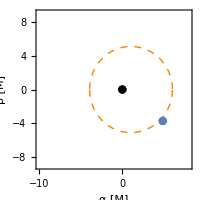

The image plane:
black——BH; orange——critical curve; blue——image

```mathematica
cc$up=ParametricPlot[{αc[rc,a,θo],βc[rc,a,θo]},{rc,rcRange[a][[1]],rcRange[a][[2]]},AspectRatio->1,Frame->True,FrameStyle->14,
FrameLabel->{StringJoin["α [",ToString@TraditionalForm[M],"]"],StringJoin["β [",ToString@TraditionalForm[M],"]"]},
LabelStyle->14,Axes->False,PlotStyle->Directive[Dashed,Orange,Thickness[0.005]],PlotPoints->100
];

cc$down=ParametricPlot[{αc[rc,a,θo],-βc[rc,a,θo]},{rc,rcRange[a][[1]],rcRange[a][[2]]},PlotStyle->Directive[Dashed,Orange,Thickness[0.005]],PlotPoints->100];
plotimage=ListPlot[{{data["α"],data["β"]}},PlotStyle->Directive[PointSize[0.03]]];
plotBH=ListPlot[{{0,0}},PlotStyle->Directive[Black,PointSize[0.03]]];
Show[cc$up,cc$down,plotimage,plotBH,PlotRange->{{-10,8},{-9,9}},ImageSize->200]
Print["The image plane:\nblack——BH; orange——critical curve; blue——image" ]
```

Stretch rates of princical axes: {0.740902,0.0412764}

Magnification rate of area: 0.0305817

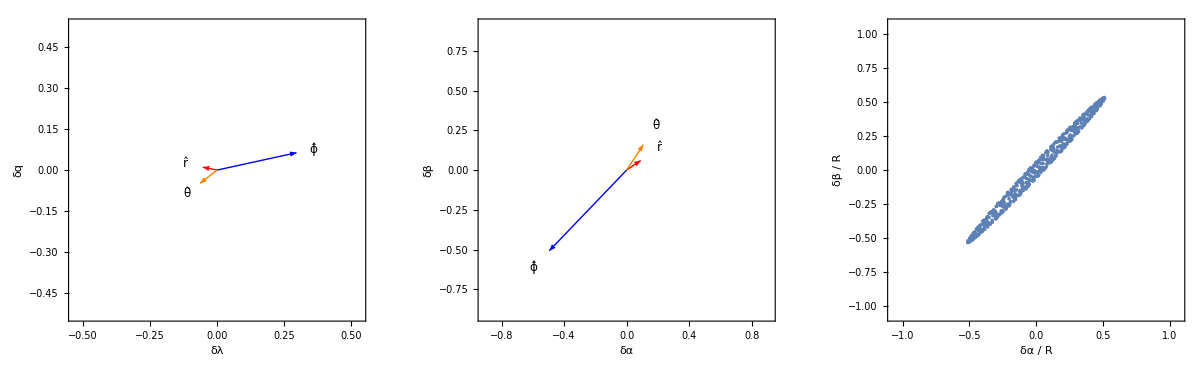
{-Graphics-,{0.740902,0.0412764,0.0305817}}

r^⋀, θ^⋀, ϕ^⋀: the unit base vectors of the spherical coordinate system, normalized to length 1.
Here they are mapped to the λ-η plane and α-β plane.

```mathematica
If[Not@StringQ@data,Shape[a,data["λ"],Sqrt[data["η"]],rs,θs,ro,data["νrs"],data["νθs"]]]
Print["r^⋀, θ^⋀, ϕ^⋀: the unit base vectors of the spherical coordinate system, normalized to length 1.\nHere they are mapped to the λ-η plane and α-β plane."]
```